```mathematica
InelasticRoot="C:\\Users\\389764\\Documents\\Inelastic";
```

## The SevenOperators package

```mathematica
minus=-1;

JNorm[j_]:=2j+1;

QNorm[j_]:=Sqrt[2 j+1];
```

triangular inequalities,conditions to have a non-zero six-j symbol and definition of our own 6J and 3J symbols:

NOTE:we define the 6J symbol (and do a similar trick for the 3J simbol) as a function that equals the built-in function SixJSymbol only if the latter is not-zero.This escamotage is done to circumvent Mathematica giving error messages and warnings

triangular inequality:

```mathematica
Triangular[x_,y_,z_]:=Abs[x-y]≤z≤x+y
```

condition on the z-projection of the momentum, m

```mathematica
RangeM[j_,m_]:=-Abs[j]≤m≤Abs[j]
```

conditions to have a non-zero six-j symbol:

```mathematica
SixJConditionTriad[j1_,j2_,j3_]:=IntegerQ[j1+j2+j3]&&Triangular[j1,j2,j3]

SixJCondition[j1_,j2_,j3_,J1_,J2_,J3_]:=SixJConditionTriad[j1,j2,j3]&&SixJConditionTriad[j1,J2,J3]&&SixJConditionTriad[J1,j2,J3]&&SixJConditionTriad[J1,J2,j3]
```

impose the condition explicitly in the definition of the six-j symbol (the condition is already included in Mathematica,but imposing it explicitly has the advantage that the six-j symbol is evaluated only if it is non-zero, and so warning messages are avoided)

```mathematica
SixJ[{j1_,j2_,j3_},{J1_,J2_,J3_}]:=Which[SixJCondition[j1,j2,j3,J1,J2,J3],SixJSymbol[{j1,j2,j3},{J1,J2,J3}],True,0]
```

conditions to have a non-zero 3-j symbol:

```mathematica
ThreeJCondition[{j1_,m1_},{j2_,m2_},{j3_,m3_}]:=Triangular[j1,j2,j3]&&RangeM[j1,m1]&&RangeM[j2,m2]&&RangeM[j3,m3]&&m1+m2+m3==0

ThreeJ[{j1_,m1_},{j2_,m2_},{j3_,m3_}]:=Which[ThreeJCondition[{j1,m1},{j2,m2},{j3,m3}],ThreeJSymbol[{j1,m1},{j2,m2},{j3,m3}],True,0]
```

Nine-j symbol:

choose the cutoff of the summation in the expression of NineJSymbol:

```mathematica
cutsum=50;

SummandNineJ[j1_,j2_,j12_,j3_,j4_,j34_,j13_,j24_,j_,g_]:=minus^(2*g) JNorm[g] SixJ[{j1,j2,j12},{j34,j,g}]*SixJ[{j3,j4,j34},{j2,g,j24}]*SixJ[{j13,j24,j},{g,j1,j3}]


NineJSymbol[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,j_}]:=Sum[SummandNineJ[j1,j2,j12,j3,j4,j34,j13,j24,j,g],{g,0,cutsum+1/2,1/2}]
```

several tests were performed.As benchmark,we used the results from the website:http://www-stone.ch.cam.ac.uk/wigner.shtml

auxiliary functions:

Bessel functions:

```mathematica
BesselFactor1[y_,{np_,lp_},{n_,l_},lcap_]:=(2^lcap)/(JNorm[lcap]!!) y^(lcap/2) Exp[-y] Sqrt[(np-1)! (n-1)!]

BesselFactor2[y_,{np_,lp_},{n_,l_},lcap_]:=Sqrt[Gamma[np+lp+1/2]*Gamma[n+l+1/2]]

Summand1[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=minus^(m+mp)/(m! mp! (n-1-m)! (np-1-mp)!)

Summand2[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=Gamma[(l+lp+lcap+2*m+2*mp+3)/2]/(Gamma[l+m+3/2]*Gamma[lp+mp+3/2])

Summand3[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=Hypergeometric1F1[(lcap-lp-l-2*mp-2*m)/2,lcap+3/2,y]

BesselFactor3[y_,{np_,lp_},{n_,l_},lcap_]:=Sum[(Summand1[y,{np,lp,mp},{n,l,m},lcap]*Summand2[y,{np,lp,mp},{n,l,m},lcap]*Summand3[y,{np,lp,mp},{n,l,m},lcap]),{m,0,n-1},{mp,0,np-1}]


BesselElement[y_,{np_,lp_},{n_,l_},lcap_]:=BesselFactor1[y,{np,lp},{n,l},lcap]*BesselFactor2[y,{np,lp},{n,l},lcap]*BesselFactor3[y,{np,lp},{n,l},lcap]
```

```mathematica
BesselFactor1A[y_,{np_,lp_},{n_,l_},lcap_]:=(2^(lcap-1))/(JNorm[lcap]!!) y^((lcap-1)/2) Exp[-y] Sqrt[(np-1)! (n-1)!]

BesselFactor2[y_,{np_,lp_},{n_,l_},lcap_]:=Sqrt[Gamma[np+lp+1/2]*Gamma[n+l+1/2]]

(**)


Summand1[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=(-1)^(m+mp)/(m! mp! (n-1-m)! (np-1-mp)!)

Summand2A[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=Gamma[(l+lp+lcap+2*m+2*mp+2)/2]/(Gamma[l+m+3/2]*Gamma[lp+mp+3/2])

Summand3A[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=-(l+lp+lcap+2*m+2*mp+2)/2*Hypergeometric1F1[(lcap-lp-l-2*mp-2*m-1)/2,lcap+3/2,y]+2*m*Hypergeometric1F1[(lcap-lp-l-2*mp-2*m+1)/2,lcap+3/2,y]


BesselFactor3A[y_,{np_,lp_},{n_,l_},lcap_]:=Sum[(Summand1[y,{np,lp,mp},{n,l,m},lcap]*Summand2A[y,{np,lp,mp},{n,l,m},lcap]*Summand3A[y,{np,lp,mp},{n,l,m},lcap]),{m,0,n-1},{mp,0,np-1}]

(**)

BesselElementMinus[y_,{np_,lp_},{n_,l_},lcap_]:=BesselFactor1A[y,{np,lp},{n,l},lcap]*BesselFactor2[y,{np,lp},{n,l},lcap]*BesselFactor3A[y,{np,lp},{n,l},lcap]


(**)

Summand4A[y_,{np_,lp_,mp_},{n_,l_,m_},lcap_]:=-(l+lp+lcap+2*m+2*mp+2)/2*Hypergeometric1F1[(lcap-lp-l-2*mp-2*m-1)/2,lcap+3/2,y]+(2*l+2*m+1)*Hypergeometric1F1[(lcap-lp-l-2*mp-2*m+1)/2,lcap+3/2,y]

BesselFactor4A[y_,{np_,lp_},{n_,l_},lcap_]:=Sum[(Summand1[y,{np,lp,mp},{n,l,m},lcap]*Summand2A[y,{np,lp,mp},{n,l,m},lcap]*Summand4A[y,{np,lp,mp},{n,l,m},lcap]),{m,0,n-1},{mp,0,np-1}]

BesselElementPlus[y_,{np_,lp_},{n_,l_},lcap_]:=BesselFactor1A[y,{np,lp},{n,l},lcap]*BesselFactor2[y,{np,lp},{n,l},lcap]*BesselFactor4A[y,{np,lp},{n,l},lcap]
```

define n and l as functions of N,J,j

```mathematica
Lnumber[NPrincipal_,j_]:=Which[EvenQ[NPrincipal-(j+1/2)],(j+1/2),True,j-1/2]

Nodal[NPrincipal_,j_]:=(NPrincipal-Lnumber[NPrincipal,j])/2+1
```

parity and parity conservation:

define parities of an individual state and of the operators:

```mathematica
ParityState[NPrincipal_,j_]:=minus^(Lnumber[NPrincipal,j])
```

normal parity:

```mathematica
ParityNormal[jcap_]:=minus^(jcap)


ParityConsNormal[NPrincipalp_,jp_,NPrincipal_,j_,jcap_]:=ParityState[NPrincipal,j]*ParityState[NPrincipalp,jp]*ParityNormal[jcap]
```

logical variable that checks that 1. parity is conserved 2. the nodal numbers are >0 , 3. the momenta J,j and j' satisfy the triangular inequality

```mathematica
PhysicalConditionsNormal[NPrincipalp_,jp_,NPrincipal_,j_,jcap_]:=ParityConsNormal[NPrincipal,j,NPrincipalp,jp,jcap]==1&&Nodal[NPrincipal,j]>0&&Nodal[NPrincipalp,jp]>0&&Abs[j-jp]≤jcap≤j+jp
```

abnormal parity:

```mathematica
ParityAbnormal[jcap_]:=minus^(jcap+1)


ParityConsAbnormal[NPrincipalp_,jp_,NPrincipal_,j_,jcap_]:=ParityState[NPrincipal,j]*ParityState[NPrincipalp,jp]*ParityAbnormal[jcap]
```

logical variable that checks that 1. parity is conserved 2. the nodal numbers are >0 ; 3. the momenta J,j and j' satisfy the triangular inequality

```mathematica
PhysicalConditionsAbnormal[NPrincipalp_,jp_,NPrincipal_,j_,jcap_]:=ParityConsAbnormal[NPrincipal,j,NPrincipalp,jp,jcap]==1&&Nodal[NPrincipal,j]>0&&Nodal[NPrincipalp,jp]>0&&Abs[j-jp]≤jcap≤j+jp
```

## Operators: normal parity

MJ :

```mathematica
mjelement[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=minus^(1/2+j+jcap) Sqrt[(JNorm[j]*JNorm[jp]*JNorm[l]*JNorm[lp]*JNorm[jcap])/(4 Pi)]*ThreeJ[{lp,0},{jcap,0},{l,0}]*SixJ[{lp,jp,1/2},{j,l,jcap}]*BesselElement[y,{np,lp},{n,l},jcap]
```

write it in terms of N,N',j,j':

```mathematica
MJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=mjelement[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is =0 if the physical conditions are not satisfied

```mathematica
MJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],MJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

SigmaJ

```mathematica
MJLSigma[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_,lcap_]:=minus^lp Sqrt[(JNorm[j]*JNorm[jp]*JNorm[l]*JNorm[lp]*JNorm[jcap]*JNorm[lcap])/(4 Pi)]*Sqrt[6]*ThreeJ[{lp,0},{lcap,0},{l,0}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}]*BesselElement[y,{np,lp},{n,l},lcap]
```

write it in terms of N,N',j,j':

```mathematica
SigmaJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=MJLSigma[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap,jcap]
```

We also impose explicitly that the function is =0 if the physical conditions are not satisfied

```mathematica
SigmaJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],SigmaJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

DeltaPJ

```mathematica
MJLDivQoverall[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_,lcap_]:=minus^(lcap+j+1/2)*QNorm[lp]*QNorm[jp]*QNorm[j]*QNorm[jcap]*QNorm[lcap]*SixJ[{lp,jp,1/2},{j,l,jcap}]/Sqrt[4 Pi]

MJLDivQsummand1[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_,lcap_]:=-Sqrt[l+1] QNorm[l+1] SixJ[{lcap,1,jcap},{l,lp,l+1}] ThreeJ[{lp,0},{lcap,0},{l+1,0}] BesselElementMinus[y,{np,lp},{n,l},lcap]

MJLDivQsummand2[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_,lcap_]:=Sqrt[l] QNorm[l-1] SixJ[{lcap,1,jcap},{l,lp,l-1}] ThreeJ[{lp,0},{lcap,0},{l-1,0}] BesselElementPlus[y,{np,lp},{n,l},lcap]



MJLDivQ[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_,lcap_]:=MJLDivQoverall[y,{np,lp,jp},{n,l,j},jcap,lcap]*(MJLDivQsummand1[y,{np,lp,jp},{n,l,j},jcap,lcap]+MJLDivQsummand2[y,{np,lp,jp},{n,l,j},jcap,lcap])

DeltaPrime[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=-Sqrt[jcap]/QNorm[jcap]*MJLDivQ[y,{np,lp,jp},{n,l,j},jcap,jcap+1]+Sqrt[jcap+1]/QNorm[jcap]*MJLDivQ[y,{np,lp,jp},{n,l,j},jcap,jcap-1]
```

write it in terms of N,N',j,j':

```mathematica
DeltaPrimeJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=DeltaPrime[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is =0 if the physical conditions are not satisfied

```mathematica
DeltaPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],DeltaPrimeJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

DeltaPPJ and DeltaTPPJ

```mathematica
DeltaPrimePrime[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=Sqrt[jcap+1]/QNorm[jcap]*MJLDivQ[y,{np,lp,jp},{n,l,j},jcap,jcap+1]+Sqrt[jcap]/QNorm[jcap]*MJLDivQ[y,{np,lp,jp},{n,l,j},jcap,jcap-1]
```

write it in terms of N,N',j,j':

```mathematica
DeltaPrimePrimeJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=DeltaPrimePrime[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is =0 if the physical conditions are not satisfied

```mathematica
DeltaPPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],DeltaPrimePrimeJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

define DeltaTPPJ

```mathematica
DeltaTPPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=DeltaPPJ[y,{ncapp,jp},{ncap,j},jcap]-MJ[y,{ncapp,jp},{ncap,j},jcap]/2
```

PhiPPJ

```mathematica
PhiPPoverall[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=minus^(lp+1)*6 *QNorm[lp]*QNorm[jp]*QNorm[j]/Sqrt[4 Pi]

PhiPPsummand1[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=QNorm[l+1]*Sqrt[l+1]*ThreeJ[{lp,0},{jcap+1,0},{l+1,0}]*BesselElementMinus[y,{np,lp},{n,l},jcap+1]*Sum[minus^(jcap-lcap+1)*JNorm[lcap]*SixJ[{jcap+1,1,lcap},{1,jcap,1}]*SixJ[{jcap+1,1,lcap},{l,lp,l+1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,jcap,jcap+1}]

PhiPPsummand2[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=If[l==0,0,QNorm[l-1]* Sqrt[l]*ThreeJ[{lp,0},{jcap+1,0},{l-1,0}]*BesselElementPlus[y,{np,lp},{n,l},jcap+1]*Sum[minus^(jcap-lcap)*JNorm[lcap]*SixJ[{jcap+1,1,lcap},{1,jcap,1}]*SixJ[{jcap+1,1,lcap},{l,lp,l-1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,jcap,jcap+1}]]

PhiPPsummand3[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=If[jcap==0,0,QNorm[l+1]*Sqrt[l+1]*ThreeJ[{lp,0},{jcap-1,0},{l+1,0}]*BesselElementMinus[y,{np,lp},{n,l},jcap-1]*Sum[minus^(jcap-lcap+1)*JNorm[lcap]*SixJ[{jcap-1,1,lcap},{1,jcap,1}]*SixJ[{jcap-1,1,lcap},{l,lp,l+1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,jcap-1,jcap}]]

PhiPPsummand4[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=If[jcap==0,0,If[l==0,0,QNorm[l-1]* Sqrt[l]*ThreeJ[{lp,0},{jcap-1,0},{l-1,0}]*BesselElementPlus[y,{np,lp},{n,l},jcap-1]*Sum[minus^(jcap-lcap)*JNorm[lcap]*SixJ[{jcap-1,1,lcap},{1,jcap,1}]*SixJ[{jcap-1,1,lcap},{l,lp,l-1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,jcap-1,jcap}]]]

PhiPPJX[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=PhiPPoverall[y,{np,lp,jp},{n,l,j},jcap]*(QNorm[jcap+1]*Sqrt[jcap+1]*(PhiPPsummand1[y,{np,lp,jp},{n,l,j},jcap]+PhiPPsummand2[y,{np,lp,jp},{n,l,j},jcap])+If[jcap==0,0,QNorm[jcap-1]*Sqrt[jcap]*(PhiPPsummand3[y,{np,lp,jp},{n,l,j},jcap]+PhiPPsummand4[y,{np,lp,jp},{n,l,j},jcap])])
```

Write PhiPP  in terms of N,N’,j,j’:

```mathematica
PhiPPJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=PhiPPJX[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is = 0 if the physical conditions are not satisfied

```mathematica
PhiPPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],PhiPPJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

PhiPJ and PhiTPJ

```mathematica
PhiPJX[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=PhiPPoverall[y,{np,lp,jp},{n,l,j},jcap]*(-QNorm[jcap+1]*Sqrt[jcap]*(PhiPPsummand1[y,{np,lp,jp},{n,l,j},jcap]+PhiPPsummand2[y,{np,lp,jp},{n,l,j},jcap])+If[jcap==0,0,QNorm[jcap-1]*Sqrt[jcap+1]*(PhiPPsummand3[y,{np,lp,jp},{n,l,j},jcap]+PhiPPsummand4[y,{np,lp,jp},{n,l,j},jcap])])
```

Write PhiP  in terms of N,N’,j,j’:

```mathematica
PhiPJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=PhiPJX[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is = 0 if the physical conditions are not satisfied

```mathematica
PhiPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsNormal[ncapp,jp,ncap,j,jcap],PhiPJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

Now evaluate PhiPT to have simple turn-around properties

```mathematica
PhiTPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=PhiPJ[y,{ncapp,jp},{ncap,j},jcap]+SigmaJ[y,{ncapp,jp},{ncap,j},jcap]/2
```

## Operators: abnormal parity

DeltaJ:

```mathematica
Deltaop[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=MJLDivQ[y,{np,lp,jp},{n,l,j},jcap,jcap]
```

write it in terms of N,N',j,j':

```mathematica
DeltaJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=Deltaop[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is=0 if the physical conditions are not satisfied

```mathematica
DeltaJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsAbnormal[ncapp,jp,ncap,j,jcap],DeltaJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

SigmaPJ :

```mathematica
SigmaPrime[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=-Sqrt[jcap]/QNorm[jcap]*MJLSigma[y,{np,lp,jp},{n,l,j},jcap,jcap+1]+Sqrt[jcap+1]/QNorm[jcap]*MJLSigma[y,{np,lp,jp},{n,l,j},jcap,jcap-1]
```

write it in terms of N,N',j,j':

```mathematica
SigmaPrimeJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=SigmaPrime[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that  the function is =0 if the physical conditions are not satisfied

```mathematica
SigmaPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsAbnormal[ncapp,jp,ncap,j,jcap],SigmaPrimeJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

SigmaPPJ:

```mathematica
SigmaSecond[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=(Sqrt[jcap+1] MJLSigma[y,{np,lp,jp},{n,l,j},jcap,jcap+1]+Sqrt[jcap] MJLSigma[y,{np,lp,jp},{n,l,j},jcap,jcap-1])/QNorm[jcap]
```

write it in terms of N,N',j,j':

```mathematica
SigmaSecondJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=SigmaSecond[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that  the function is =0 if the physical conditions are not satisfied

```mathematica
SigmaPPJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsAbnormal[ncapp,jp,ncap,j,jcap],SigmaSecondJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

OmegaJ and OmegaTJ:

```mathematica
MJLDivSigoverall[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=minus^(lp)*QNorm[lp]*QNorm[jp]*QNorm[j]*QNorm[2 j-l]*QNorm[jcap]*SixJ[{lp,jp,1/2},{j,2j-l,jcap}]*ThreeJ[{lp,0},{jcap,0},{2j-l,0}]/Sqrt[4 Pi]

MJLDivSigsummand1[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=-KroneckerDelta[j,l+1/2]*BesselElementMinus[y,{np,lp},{n,l},jcap]

MJLDivSigsummand2[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=KroneckerDelta[j,l-1/2]*BesselElementPlus[y,{np,lp},{n,l},jcap]

MJLDivSig[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=MJLDivSigoverall[y,{np,lp,jp},{n,l,j},jcap]*(MJLDivSigsummand1[y,{np,lp,jp},{n,l,j},jcap]+MJLDivSigsummand2[y,{np,lp,jp},{n,l,j},jcap])
```

write Omega  in terms of N,N',j,j':

```mathematica
OmegaJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=MJLDivSig[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that  the function is =0 if the physical conditions are not satisfied

```mathematica
OmegaJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsAbnormal[ncapp,jp,ncap,j,jcap],OmegaJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

define OmegaTJ

```mathematica
OmegaTJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=OmegaJ[y,{ncapp,jp},{ncap,j},jcap]+SigmaPPJ[y,{ncapp,jp},{ncap,j},jcap]/2
```

PhiJ and PhiTJ:

```mathematica
Phioverall[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=minus^(lp+1)*6 *QNorm[lp]*QNorm[jp]*QNorm[j]*JNorm[jcap]/Sqrt[4 Pi]

Phisummand1[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=QNorm[l+1]*Sqrt[l+1]*ThreeJ[{lp,0},{jcap,0},{l+1,0}]*BesselElementMinus[y,{np,lp},{n,l},jcap]*Sum[minus^(jcap-lcap+1)*JNorm[lcap]*SixJ[{jcap,1,lcap},{1,jcap,1}]*SixJ[{jcap,1,lcap},{l,lp,l+1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,Max[0,jcap-1],jcap+1}]

Phisummand2[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=If[l==0,0,QNorm[l-1]* Sqrt[l]*ThreeJ[{lp,0},{jcap,0},{l-1,0}]*BesselElementPlus[y,{np,lp},{n,l},jcap]*Sum[minus^(jcap-lcap)*JNorm[lcap]*SixJ[{jcap,1,lcap},{1,jcap,1}]*SixJ[{jcap,1,lcap},{l,lp,l-1}]*NineJSymbol[{lp,l,lcap},{1/2,1/2,1},{jp,j,jcap}],{lcap,Max[0,jcap-1],jcap+1}]]

PhiJX[y_,{np_,lp_,jp_},{n_,l_,j_},jcap_]:=Phioverall[y,{np,lp,jp},{n,l,j},jcap]*(Phisummand1[y,{np,lp,jp},{n,l,j},jcap]+Phisummand2[y,{np,lp,jp},{n,l,j},jcap])
```

write Phi  in terms of N,N’,j,j’:

```mathematica
PhiJE[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=PhiJX[y,{Nodal[ncapp,jp],Lnumber[ncapp,jp],jp},{Nodal[ncap,j],Lnumber[ncap,j],j},jcap]
```

We also impose explicitly that the function is = 0 if the physical conditions are not satisfied

```mathematica
PhiJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=If[PhysicalConditionsAbnormal[ncapp,jp,ncap,j,jcap],PhiJE[y,{ncapp,jp},{ncap,j},jcap],0]
```

Now evaluate PhiT to have simple turn-around properties

```mathematica
PhiTJ[y_,{ncapp_,jp_},{ncap_,j_},jcap_]:=PhiJ[y,{ncapp,jp},{ncap,j},jcap]-SigmaPJ[y,{ncapp,jp},{ncap,j},jcap]/2
```

Now let’s establish all of the nuclear physics input.

```mathematica
(*Number of final states*) NumFS=4;
```

```mathematica
A=27;
Abar=A;
```

```mathematica
JSI={5/2,5/2,5/2,5/2};
```

```mathematica
JSF={5/2,1/2,3/2,7/2};
```

```mathematica
TMTS={1/2,-1/2};
```

```mathematica
MuCapRate=0.6982 *10^6;
```

```mathematica
(*Input oscillator parameter*) b=Sqrt[41.467/(45Abar^(-1/3) -25Abar^(-2/3))]; 
Print["Oscillator parameter = ",b," fermis"];b=b/197.3269718;
```

Oscillator parameter = 1.84194 fermis

```mathematica
(*Input masses; mN is the nucleon mass;Delta is the mass defect in MeV from Nuclear Wallet Cards, 931.494028 is the 12C mass unit; Masses is the resulting array of nuclear masses in MeV*) mN=939.;Delta=
-17.197;
Mbar=Delta + 931.494028*Abar;
```

```mathematica
mumass=105.6583755;
emass=0.511;
alpha=1/(137.035999082);
hbar=6.5821 10^(-22);
Nmass=939.;
mu=mumass Mbar/(mumass+Mbar);
```

```mathematica
Zval=13;
```

```mathematica
Ebind=.462953;
```

```mathematica
ΔENuc={0,0.84376,1.01456,2.21201};
```

```mathematica
qval=Table[Sqrt[Mbar/(mumass+Mbar) ((mumass-Ebind-ΔENuc[[is]])^2-emass^2)],{is,1,Length[ΔENuc]}];
```

```mathematica
qeff=110.809-ΔENuc;
```

```mathematica
Zeffel=0.657^(1/3)*13; 
(* Effective nuclear charge for inelastic transitions *) Zeffin=0.604^(1/3)*13 ;
(* Muon wave function |Subscript[ϕ, 1s]^Subscript[Z, eff](0)|^2*) RZ2el= (Zeffel  alpha  mu)^3/Pi;
RZ2in= (Zeffin  alpha  mu)^3/Pi;
RZ2={RZ2el,RZ2in,RZ2in,RZ2in};
```

```mathematica
Print["  Z = ",Zval,"   Zeff_el = ",Zeffel,"   Zeff_inel = ",Zeffin];
Print["  Momentum transfer to electron = ",qval,"MeV     qeff = ",qeff," MeV"];
Print["  muon binding energy = ",Ebind," MeV"]
```

Z = 13   Zeff_el = 11.3014   Zeff_inel = 10.9889

Momentum transfer to electron = {104.974,104.132,103.961,102.766}MeV     qeff = {110.809,109.965,109.794,108.597} MeV

muon binding energy = 0.462953 MeV

```mathematica
(*Directory of input DM files; [i,j,k] i is the nucleus (Ncode); j is the isotope; k is the interaction*) 
DMstring[1,1]=StringJoin[InelasticRoot,"\\Densities\\Al27_bw_0_0.txt"];
DMstring[1,2]=StringJoin[InelasticRoot,"\\Densities\\Al27_bw_0_1.txt"];
DMstring[1,3]=StringJoin[InelasticRoot,"\\Densities\\Al27_bw_0_2.txt"];
DMstring[1,4]=StringJoin[InelasticRoot,"\\Densities\\Al27_bw_0_3.txt"];

DMstring[2,1]=StringJoin[InelasticRoot,"\\Densities\\Al27_usda_0_0.txt"];
DMstring[2,2]=StringJoin[InelasticRoot,"\\Densities\\Al27_usda_0_1.txt"];
DMstring[2,3]=StringJoin[InelasticRoot,"\\Densities\\Al27_usda_0_2.txt"];
DMstring[2,4]=StringJoin[InelasticRoot,"\\Densities\\Al27_usda_0_3.txt"];

DMstring[3,1]=StringJoin[InelasticRoot,"\\Densities\\Al27_usdb_0_0.txt"];
DMstring[3,2]=StringJoin[InelasticRoot,"\\Densities\\Al27_usdb_0_1.txt"];
DMstring[3,3]=StringJoin[InelasticRoot,"\\Densities\\Al27_usdb_0_2.txt"];
DMstring[3,4]=StringJoin[InelasticRoot,"\\Densities\\Al27_usdb_0_3.txt"];
```

```mathematica
DMLoad[ISM_]:=Module[{},
Clear[DM];Do[DMin=ReadList[DMstring[ISM,iFS],Number,RecordLists->True];
LcMax=Length[DMin];
jj=0;
Do[
If[Length[DMin[[Lc]]]==6,(jj=jj+1;NumDMs[iFS]=jj;kk=0;JF[iFS]=DMin[[Lc,1]]/2;TF[iFS]=DMin[[Lc,2]]/2;JI[iFS]=DMin[[Lc,3]]/2;TI[iFS]=DMin[[Lc,4]]/2;J0[iFS,jj]=DMin[[Lc,5]]/2;T0[iFS,jj]=DMin[[Lc,6]]/2;
If[JF[iFS]==JSF[[iFS]],True,Abort[]];
If[TF[iFS]==TMTS[[1]],True,Abort[]];
If[JI[iFS]==JSI[[iFS]],True,Abort[]];
If[TI[iFS]==TMTS[[1]],True,Abort[]]),True]
If[Length[DMin[[Lc]]]==5,(kk=kk+1;LDM[iFS,jj]=kk;
NB[iFS,jj,kk]=DMin[[Lc,1]];JB[iFS,jj,kk]=DMin[[Lc,2]]/2;NK[iFS,jj,kk]=DMin[[Lc,3]];JK[iFS,jj,kk]=DMin[[Lc,4]]/2;DMval[iFS,jj,kk]=DMin[[Lc,5]]),True],
{Lc,1,LcMax}];
Do[DM[iFS,jj]=Table[{{NB[iFS,jj,kk],JB[iFS,jj,kk]},{NK[iFS,jj,kk],JK[iFS,jj,kk]},DMval[iFS,jj,kk]},{kk,1,LDM[iFS,jj]}],{jj,1,NumDMs[iFS]}];,
{iFS,1,NumFS}]]
```

```mathematica
ISOT[TT_,MT_,T0_]:=KroneckerDelta[T0,0]Sqrt[2]/QNorm[TT]+KroneckerDelta[T0,1]  If[MT==0,0,MT Sqrt[6 /((2TT+1)(TT+1)TT)]]
```

```mathematica
Clear[FM]
```

```mathematica
FM[iFS_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[iFS,jj]]Sum[DM[iFS,jj][[kk,3]] MJ[y,DM[iFS,jj][[kk,1]],DM[iFS,jj][[kk,2]],J0[iFS,jj]],{kk,1,LDM[iFS,jj]}]
```

```mathematica
(*Check J=0 T=0,1 DMs by evaluating the A and Z-N sum rules*)Do[Do[If[J0[iFS,jj]==0,(Valu=Sqrt[4 Pi/(2JI[iFS]+1)]FM[iFS,jj,0.00000001];Print["J0 = ",J0[iFS,jj],"  T0 = ",T0[iFS,jj],"  Charge = ",Valu]),True],{jj,1,NumDMs[iFS]}],
{iFS,1,Length[ΔENuc]}]
```

J0 = 0  T0 = 0  Charge = 27.

J0 = 0  T0 = 1  Charge = -0.999999

```mathematica
FPhiPP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] PhiPPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

Let’s now do the spin-dependent guys:

```mathematica
FSigmaPP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] SigmaPPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FDelta[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] DeltaJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FDeltaP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] DeltaPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FDeltaTPP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] DeltaTPPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FSigmaP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] SigmaPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FSigma[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] SigmaJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FOmegaT[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] OmegaTJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FPhiTP[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] PhiTPJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
FPhiT[ii_,jj_,y_]:=ISOT[TMTS[[1]],TMTS[[2]],T0[ii,jj]]Sum[DM[ii,jj][[kk,3]] PhiTJ[y,DM[ii,jj][[kk,1]],DM[ii,jj][[kk,2]],J0[ii,jj]],{kk,1,LDM[ii,jj]}]
```

```mathematica
(*Now define the effective theory input, with the isospin indices {isoscalar,isovector} specified by {i,j}*) RM[i_,j_,cs_]:= cs[1,i]Conjugate[cs[1,j]] + cs[11,i] Conjugate[cs[11,j]]
```

```mathematica
RPhiPP[i_,j_,cs_]:=  cs[3,i] Conjugate[cs[3,j]] + (cs[12,i]- cs[15,i]) Conjugate[cs[12,j]- cs[15,j]]
```

```mathematica
RPhiPPM[i_,j_,cs_]:=Re[ cs[3,i]Conjugate[cs[1,j]] - (cs[12,i]-cs[15,i]) Conjugate[cs[11,j]]]
```

```mathematica
RPhiTP[i_,j_,cs_]:= cs[12,i] Conjugate[cs[12,j]] + cs[13,i] Conjugate[cs[13,j]]
```

```mathematica
RPhiT[i_,j_,cs_]:= RPhiTP[i,j,cs]
```

```mathematica
RSigmaPP[i_,j_,cs_]:=cs[10,i] Conjugate[cs[10,j]] +(cs[4,i]-cs[6,i])Conjugate[ cs[4,j]-cs[6,j]]
```

```mathematica
RSigmaP[i_,j_,cs_]:=cs[4,i] Conjugate[cs[4,j]]+  cs[9,i] Conjugate[cs[9,j]]
```

```mathematica
RDelta[i_,j_,cs_]:= cs[5,i] Conjugate[cs[5,j]] +cs[8,i] Conjugate[cs[8,j]]
```

```mathematica
RDeltaSigmaP[i_,j_,cs_]:= Re[cs[5,i] Conjugate[cs[4,j]]+ cs[8,i]Conjugate[cs[9,j]]]
```

```mathematica
ROmegaT[i_,j_,cs_]:= cs[7,i] Conjugate[cs[7,j]]+ cs[14,i]Conjugate[cs[14,j]]
```

```mathematica
RDeltaTPP[i_,j_,cs_]:= cs[2,i] Conjugate[cs[2,j]]+ (cs[8,i]-cs[16,i])*Conjugate[cs[8,j]-cs[16,j]]
```

```mathematica
RDeltaTPPM[i_,j_,cs_]:=Im[ cs[2,i] Conjugate[cs[1,j]]- (cs[8,i]-cs[16,i])*Conjugate[cs[11,j]]]
```

```mathematica
RDeltaTPPPhiPP[i_,j_,cs_]:= Im[cs[2,i] Conjugate[cs[3,j]]+ (cs[8,i]-cs[16,i])*Conjugate[cs[12,j]-cs[15,j]]]
```

```mathematica
ROmegaTSigmaPP[i_,j_,cs_]:= Im[cs[7,i]*Conjugate[cs[10,j]]-cs[14,i]* Conjugate[cs[4,j]-cs[6,j] ]]
```

```mathematica
RDeltaPhiT[i_,j_,cs_]:=Im[ cs[5,i] Conjugate[cs[13,j]]+ cs[8,i]*Conjugate[cs[12,j]]]
```

```mathematica
RPhiTPSigma[i_,j_,cs_]:=Im[cs[13,i] Conjugate[cs[4,j]]+ cs[12,i]*Conjugate[cs[9,j]]]
```

```mathematica
(*We now calculate the total response functions, summed over isotopes, weighted by the abundance,again with very small kinematic differences between isotopes due to masses ignored, to be later approximated by an effecive average nuclear mass*)WM[iFS_,qm_,y_,cs_]:=(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RM[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FM[iFS,jj,y] FM[iFS,jjp,y]RM[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiPP[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiPP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FPhiPP[iFS,jj,y] FPhiPP[iFS,jjp,y]RPhiPP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiPPM[iFS_,qm_,y_,cs_]:=-2 qm *4 Pi/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiPPM[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FPhiPP[iFS,jj,y] FM[iFS,jjp,y]RPhiPPM[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaTPPM[iFS_,qm_,y_,cs_]:=2 qm *4 Pi/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaTPPM[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDeltaTPP[iFS,jj,y] FM[iFS,jjp,y]RDeltaTPPM[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaTPPPhiPP[iFS_,qm_,y_,cs_]:=2 qm^2 *4 Pi/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaTPPPhiPP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0), FDeltaTPP[iFS,jj,y]FPhiPP[iFS,jjp,y]RDeltaTPPPhiPP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiTP[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiTP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FPhiTP[iFS,jj,y] FPhiTP[iFS,jjp,y]RPhiTP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiT[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiT[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FPhiT[iFS,jj,y] FPhiT[iFS,jjp,y]RPhiT[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WOmegaT[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(ROmegaT[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FOmegaT[iFS,jj,y] FOmegaT[iFS,jjp,y]ROmegaT[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WSigmaPP[iFS_,qm_,y_,cs_]:=(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RSigmaPP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FSigmaPP[iFS,jj,y] FSigmaPP[iFS,jjp,y]RSigmaPP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDelta[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDelta[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDelta[iFS,jj,y] FDelta[iFS,jjp,y]RDelta[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaP[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDelta[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDeltaP[iFS,jj,y] FDeltaP[iFS,jjp,y]RDelta[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaTPP[iFS_,qm_,y_,cs_]:=qm^2 *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaTPP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDeltaTPP[iFS,jj,y] FDeltaTPP[iFS,jjp,y]RDeltaTPP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WSigmaP[iFS_,qm_,y_,cs_]:=(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RSigmaP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FSigmaP[iFS,jj,y] FSigmaP[iFS,jjp,y]RSigmaP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WSigma[iFS_,qm_,y_,cs_]:=(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RSigmaP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FSigma[iFS,jj,y] FSigma[iFS,jjp,y]RSigmaP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaSigmaP[iFS_,qm_,y_,cs_]:=-2 qm *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaSigmaP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDelta[iFS,jj,y] FSigmaP[iFS,jjp,y]RDeltaSigmaP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaPSigma[iFS_,qm_,y_,cs_]:=2 qm *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaSigmaP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDeltaP[iFS,jj,y] FSigma[iFS,jjp,y]RDeltaSigmaP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WOmegaTSigmaPP[iFS_,qm_,y_,cs_]:=-2 qm *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(ROmegaTSigmaPP[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0), FOmegaT[iFS,jj,y]FSigmaPP[iFS,jjp,y]ROmegaTSigmaPP[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaPhiT[iFS_,qm_,y_,cs_]:=2 qm^2 *4 Pi/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaPhiT[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDelta[iFS,jj,y] FPhiT[iFS,jjp,y]RDeltaPhiT[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WDeltaPPhiTP[iFS_,qm_,y_,cs_]:=2 qm^2 *4 Pi/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RDeltaPhiT[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0),FDeltaP[iFS,jj,y] FPhiTP[iFS,jjp,y]RDeltaPhiT[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiTSigmaP[iFS_,qm_,y_,cs_]:=2 qm *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiTPSigma[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0), FPhiT[iFS,jj,y]FSigmaP[iFS,jjp,y]RPhiTPSigma[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
WPhiTPSigma[iFS_,qm_,y_,cs_]:=-2 qm *(4 Pi)/(2JI[iFS]+1)Sum[If[J0[iFS,jj]==J0[iFS,jjp]&&(RPhiTPSigma[T0[iFS,jj],T0[iFS,jjp],cs]!=0.0), FPhiTP[iFS,jj,y]FSigma[iFS,jjp,y]RPhiTPSigma[T0[iFS,jj],T0[iFS,jjp],cs],0],{jjp,1,NumDMs[iFS]},{jj,1,NumDMs[iFS]}]
```

```mathematica
qm=qeff/Nmass;
y=Table[(qeff[[iFS]]* b/2)^2,{iFS,1,NumFS}];
```

```mathematica
Heff[iFS_,qm_,y_,cs_]:=Module[{Wtot},
Wtot=0.0;

Wtot+=WM[iFS,qm,y,cs]+WSigmaPP[iFS,qm,y,cs]+WSigma[iFS,qm,y,cs]+WSigmaP[iFS,qm,y,cs];

Wtot+=WDeltaTPP[iFS,qm,y,cs]+WOmegaT[iFS,qm,y,cs]+WPhiPP[iFS,qm,y,cs]+WDeltaTPPPhiPP[iFS,qm,y,cs]+WDelta[iFS,qm,y,cs]+WDeltaP[iFS,qm,y,cs]+WPhiTP[iFS,qm,y,cs]+WPhiT[iFS,qm,y,cs]+WDeltaPhiT[iFS,qm,y,cs]+WDeltaPPhiTP[iFS,qm,y,cs];

Wtot+=WDeltaTPPM[iFS,qm,y,cs]+WPhiPPM[iFS,qm,y,cs]+WOmegaTSigmaPP[iFS,qm,y,cs]+WDeltaSigmaP[iFS,qm,y,cs]+WDeltaPSigma[iFS,qm,y,cs]+WPhiTPSigma[iFS,qm,y,cs]+WPhiTSigmaP[iFS,qm,y,cs];

Return[Wtot];
];
```

```mathematica
mv=246200 (*this is the weak scale in MeV, sqrt[1/(Sqrt[2]GF)], our normalization for the EFT's LECs*);
```

```mathematica
Clear[cs];Do[cs[i,0]=0;cs[i,1]=0,{i,1,16}];
```

```mathematica
A=Input["Input nonzero nonrelativistic ci coefficients as {i,ci[0],ci[1]} 
successively, \n
for i=1,3,4,5,....16 as needed \n
Inputting i=0 terminates the input \n
Input can be numerical or symbolic \n
The first coupling is isoscalar, the second is isovector \n
Thus {i,ci[0],0} is a symbolic S.D. isoscalar coupling of strength ci[0] \n
{i,0,ci[1]} is a symbolic S.D. isovector coupling of strength ci[1] \n
{i,cip/2,cip/2} is a symbolic S.D. proton only coupling of stength cip  \n
{i,cin/2,-cin/2} is a symbolic S.D. neutron only coupling of strength cin \n \n
Input desired {i,ci[0],ci[1]} now",];
i=A[[1]];
cs[i,0]=A[[2]];
cs[i,1]=A[[3]];
Do[A=Input["Input {i,ci[0],ci[1]} now",];i=A[[1]];If[i==0,Break[]];cs[i,0]=A[[2]];cs[i,1]=A[[3]],{jj,2,16}];
Print["cs values"];Do[Print["   i ",i,"  {",cs[i,0],",",cs[i,1],"}"],{i,1,16}]
```

cs values

i 1  {0,0}

i 2  {0,0}

i 3  {0,0}

i 4  {-1,10}

i 5  {0,0}

i 6  {4,-2}

i 7  {0,0}

i 8  {0,0}

i 9  {0,0}

i 10  {0,0}

i 11  {0,0}

i 12  {0,0}

i 13  {1,-1}

i 14  {0,0}

i 15  {0,0}

i 16  {0,0}

```mathematica
DMLoad[1];
DecayrateBW=Table[1/(mv^4 2  Pi) RZ2[[iFs]]*qeff[[iFs]]^2/(1+qval[[iFs]]/Mbar)*Heff[iFs,qm[[iFs]],y[[iFs]],cs]/hbar ,{iFs,1,NumFS}];
Print["  Decay rate = ",DecayrateBW,"/sec"]
```

Decay rate = {1.58693×10^6,213750.,195839.,393706.}/sec

```mathematica
DMLoad[2];
DecayrateUSDA=Table[1/(mv^4 2  Pi) RZ2[[iFs]]*qeff[[iFs]]^2/(1+qval[[iFs]]/Mbar)*Heff[iFs,qm[[iFs]],y[[iFs]],cs]/hbar ,{iFs,1,NumFS}];
Print["  Decay rate = ",DecayrateUSDA,"/sec"]
```

Decay rate = {1.35672×10^6,209198.,219786.,387503.}/sec

```mathematica
DMLoad[3];
DecayrateUSDB=Table[1/(mv^4 2  Pi) RZ2[[iFs]]*qeff[[iFs]]^2/(1+qval[[iFs]]/Mbar)*Heff[iFs,qm[[iFs]],y[[iFs]],cs]/hbar ,{iFs,1,NumFS}];
Print["  Decay rate = ",DecayrateUSDB,"/sec"]
```

Decay rate = {1.29174×10^6,218041.,217097.,381731.}/sec

```mathematica
MCR=MuCapRate;
Print["  Muon capture rate = ",MCR,"/sec"]
```

Muon capture rate = 698200./sec

```mathematica
BRBW=DecayrateBW/MuCapRate;
BRUSDA=DecayrateUSDA/MuCapRate;
BRUSDB=DecayrateUSDB/MuCapRate;
```

```mathematica
Print["  Branching ratio = ",DecayrateBW/MCR]
```

Branching ratio = {2.27289,0.306144,0.280491,0.563888}

```mathematica
BRAvg=Table[PlusMinus[Mean[{BRBW[[is]],BRUSDA[[is]],BRUSDB[[is]]}],StandardDeviation[{BRBW[[is]],BRUSDA[[is]],BRUSDB[[is]]}]],{is,1,NumFS}]
```

{2.02205±0.222156,0.30602±0.00633376,0.302073±0.018789,0.555209±0.00857737}

```mathematica
If[BRAvg[[1,1]]!=0.0,RelRatio=Table[PlusMinus[BRAvg[[iFs,1]]/BRAvg[[1,1]],Sqrt[BRAvg[[iFs,2]]^2/BRAvg[[1,1]]^2+BRAvg[[iFs,1]]^2/BRAvg[[1,1]]^4*BRAvg[[1,2]]^2]],{iFs,2,4}]]
```

{0.151341±0.0169198,0.149389±0.0188607,0.274577±0.0304637}

```mathematica
Mu2eResponseCE=Import[StringJoin[InelasticRoot,"\\Mu2e Data\\mu2e_response_CE.txt"],"Table"];
Mu2eResponseCE=Table[{Mu2eResponseCE[[is,1]],PlusMinus[Mu2eResponseCE[[is,2]],Mu2eResponseCE[[is,3]]]},{is,1,Length[Mu2eResponseCE]}];

Mu2eResponseDIO=Import[StringJoin[InelasticRoot,"\\Mu2e Data\\mu2e_response_DIO.txt"],"Table"];
Mu2eResponseDIO=Table[{PlusMinus[Mu2eResponseDIO[[is,1]],0.025],PlusMinus[Mu2eResponseDIO[[is,2]],Mu2eResponseDIO[[is,3]]]},{is,1,Length[Mu2eResponseDIO]}];
```

```mathematica
ShiftSignal[Mu2eResponse_,ΔE_,BR_]:=Module[{nShift,Mu2eShift},
nShift=Ceiling[ΔE/0.05];
Mu2eShift={};
Do[
If[is<Length[Mu2eResponse]-nShift,
AppendTo[Mu2eShift,{Mu2eResponse[[is,1]],PlusMinus[BR[[1]]*Mu2eResponse[[is+nShift,2,1]],Sqrt[BR[[2]]^2*Mu2eResponse[[is+nShift,2,1]]^2+BR[[1]]^2*Mu2eResponse[[is+nShift,2,2]]^2]]}];
,AppendTo[Mu2eShift,{Mu2eResponse[[is,1]],PlusMinus[0,0]}]];
,{is,1,Length[Mu2eResponse]}];
Return[Mu2eShift];
]
```

```mathematica
CESpectrumGS=Mu2eResponseCE;
CESpectrumEX1=ShiftSignal[CESpectrumGS,ΔENuc[[2]],RelRatio[[1]]];
CESpectrumEX2=ShiftSignal[CESpectrumGS,ΔENuc[[3]],RelRatio[[2]]];
CESpectrumEX3=ShiftSignal[CESpectrumGS,ΔENuc[[4]],RelRatio[[3]]];
CESpectrumCombined=Table[{CESpectrumGS[[is,1]],PlusMinus[CESpectrumGS[[is,2,1]]+CESpectrumEX1[[is,2,1]]+CESpectrumEX2[[is,2,1]]+CESpectrumEX3[[is,2,1]],Sqrt[CESpectrumGS[[is,2,2]]^2+CESpectrumEX1[[is,2,2]]^2+CESpectrumEX2[[is,2,2]]^2+CESpectrumEX3[[is,2,2]]^2]]},{is,1,Length[CESpectrumGS]}];
```

```mathematica
CESpectrumGSL=Table[{CESpectrumGS[[is,1]]-0.025,CESpectrumGS[[is,2,1]]},{is,1,Length[CESpectrumGS]}];
CESpectrumEX1L=Table[{CESpectrumEX1[[is,1]]-0.025,CESpectrumEX1[[is,2,1]]},{is,1,Length[CESpectrumEX1]}];
CESpectrumEX2L=Table[{CESpectrumEX2[[is,1]]-0.025,CESpectrumEX2[[is,2,1]]},{is,1,Length[CESpectrumEX2]}];
CESpectrumEX3L=Table[{CESpectrumEX3[[is,1]]-0.025,CESpectrumEX3[[is,2,1]]},{is,1,Length[CESpectrumEX3]}];
CESpectrumCombinedL=Table[{CESpectrumCombined[[is,1]]-0.025,CESpectrumCombined[[is,2,1]]},{is,1,Length[CESpectrumCombined]}];
```

```mathematica
Aspectx=1/2;
FLSx=16;
FTSx=16;

tlong=0.01;
tshort=0.005;
ticksL={{0.0,"0.0",{tlong,0}},{0.01,"",{tshort,0}},{0.02,"",{tshort,0}},{0.03,"",{tshort,0}},{0.04,"",{tshort,0}},{0.05,"",{tshort,0}},{0.06,"",{tshort,0}},{0.07,"",{tshort,0}},{0.08,"",{tshort,0}},{0.09,"",{tshort,0}},{0.1,"0.1",{tlong,0}},{0.11,"",{tshort,0}},{0.12,"",{tshort,0}},{0.13,"",{tshort,0}},{0.14,"",{tshort,0}},{0.15,"",{tshort,0}},{0.16,"",{tshort,0}},{0.17,"",{tshort,0}},{0.18,"",{tshort,0}},{0.19,"",{tshort,0}},{0.20,"0.2",{tlong,0}},{0.21,"",{tshort,0}},{0.22,"",{tshort,0}},{0.23,"",{tshort,0}},{0.24,"",{tshort,0}},{0.25,"",{tshort,0}},{0.26,"",{tshort,0}},{0.27,"",{tshort,0}},{0.28,"",{tshort,0}},{0.29,"",{tshort,0}},{0.30,"0.3",{tlong,0}},{0.31,"",{tshort,0}},{0.32,"",{tshort,0}},{0.33,"",{tshort,0}},{0.34,"",{tshort,0}},{0.35,"",{tshort,0}},{0.36,"",{tshort,0}},{0.37,"",{tshort,0}},{0.38,"",{tshort,0}},{0.39,"",{tshort,0}}};
ticksU={{0.0,"",{tlong,0}},{0.01,"",{tshort,0}},{0.02,"",{tshort,0}},{0.03,"",{tshort,0}},{0.04,"",{tshort,0}},{0.05,"",{tshort,0}},{0.06,"",{tshort,0}},{0.07,"",{tshort,0}},{0.08,"",{tshort,0}},{0.09,"",{tshort,0}},{0.1,"",{tlong,0}},{0.11,"",{tshort,0}},{0.12,"",{tshort,0}},{0.13,"",{tshort,0}},{0.14,"",{tshort,0}},{0.15,"",{tshort,0}},{0.16,"",{tshort,0}},{0.17,"",{tshort,0}},{0.18,"",{tshort,0}},{0.19,"",{tshort,0}},{0.20,"",{tlong,0}},{0.21,"",{tshort,0}},{0.22,"",{tshort,0}},{0.23,"",{tshort,0}},{0.24,"",{tshort,0}},{0.25,"",{tshort,0}},{0.26,"",{tshort,0}},{0.27,"",{tshort,0}},{0.28,"",{tshort,0}},{0.29,"",{tshort,0}},{0.30,"",{tlong,0}},{0.31,"",{tshort,0}},{0.32,"",{tshort,0}},{0.33,"",{tshort,0}},{0.34,"",{tshort,0}},{0.35,"",{tshort,0}},{0.36,"",{tshort,0}},{0.37,"",{tshort,0}},{0.38,"",{tshort,0}},{0.39,"",{tshort,0}}};
```

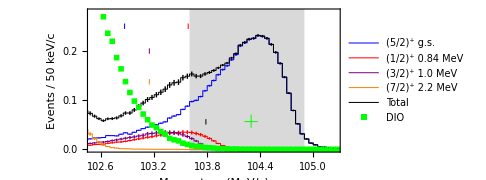

```mathematica
Show[{ListPlot[{CESpectrumGSL,CESpectrumGS},Frame->True,PlotRange->{{102.5,105.25},{0,0.28}},Joined->{True,False},InterpolationOrder->0,FrameLabel->{Style["Momentum (MeV/c)",FLSx,Black],Style["Events / 50 keV/c",FLSx,Black]},ImageSize->Medium,AspectRatio->Aspectx,PlotStyle->{{Blue,Thickness[0.002]},{Blue,AbsolutePointSize[0.00001]}},PlotMarkers->{None,None,None,None,None,None},Prolog->{LightGray,Rectangle[{103.6,-1},{104.9,+1}]},FrameTicksStyle->{{{FTSx,Black},{FTSx,Black}},{{FTSx,Black},{FTSx,Black}}},IntervalMarkers->"Bars",FrameTicks->{{ticksL,ticksU},{Automatic,Automatic}},PlotLegends->Placed[{Style["(5/2)^+  g.s.",10,Black]},Scaled[{0.2,0.88}]],Epilog->{{Directive[{Thickness[0.002],Blue}],Line[{{102.865,0.245},{102.865,0.256}}]},{Directive[{Thickness[0.002],Red}],Line[{{103.585,0.245},{103.585,0.256}}]},{Directive[{Thickness[0.002],Purple}],Line[{{103.145,0.242-0.0475},{103.145,0.253-0.0475}}]},{Directive[{Thickness[0.002],Orange}],Line[{{103.145,0.242-0.068-0.042},{103.145,0.253-0.068-0.042}}]},{Directive[{Thickness[0.002],Black}],Line[{{104.03-0.245,0.075+0.002-0.0265},{104.03-0.245,0.075+0.011+0.002-0.0265}}]},{Directive[{Thickness[0.002],Green}],Line[{{104.382-0.085,0.075-0.004-0.027},{104.382-0.085,0.075+0.011+0.01-0.025}}]},{Directive[{Thickness[0.002],Green}],Line[{{104.382-0.075-0.085,0.083-0.0265},{104.382+0.075-0.085,0.083-0.0265}}]}}],ListPlot[{CESpectrumEX1L,CESpectrumEX1},PlotStyle->{{Red,Thickness[0.002]},{Red,AbsolutePointSize[0.00001]}},PlotLegends->Placed[{Style["(1/2)^+ 0.84 MeV",10,Black]},Scaled[{0.5,0.88}]],Joined->{True,False},InterpolationOrder->0],ListPlot[{CESpectrumEX2L,CESpectrumEX2},PlotStyle->{{Purple,Thickness[0.002]},{Purple,AbsolutePointSize[0.00001]}},Joined->{True,False},InterpolationOrder->0,PlotLegends->Placed[{Style["(3/2)^+ 1.0 MeV",10,Black]},Scaled[{0.33,0.7}]]],ListPlot[{CESpectrumEX3L,CESpectrumEX3},PlotStyle->{{Orange,Thickness[0.002]},{Orange,AbsolutePointSize[0.00001]}},Joined->{True,False},InterpolationOrder->0,PlotLegends->Placed[{Style["(7/2)^+ 2.2 MeV",10,Black]},Scaled[{0.33,0.48}]]],ListPlot[{CESpectrumCombinedL,Mu2eResponseDIO,CESpectrumCombined},PlotStyle->{{Black,Thickness[0.002]},Green,{Black,AbsolutePointSize[0.00001]}},PlotMarkers->{None,■,None},Joined->{True,False,False},InterpolationOrder->0,PlotLegends->Placed[LineLegend[{Style["Total",10,Black],Style["DIO",10,Black]},LegendLayout->"Row"],Scaled[{0.6,0.2}]]]}]
```